N = 1000

λ_1 = 5.30468

λ_N = 287.289

V_spec = 14.0446

P_spec = abc = 3.3529

Window min/max: {0.,0.999998}

Fw min/max: {-4.1812,4.46059}

Length spectrum computed on 12001 grid points.

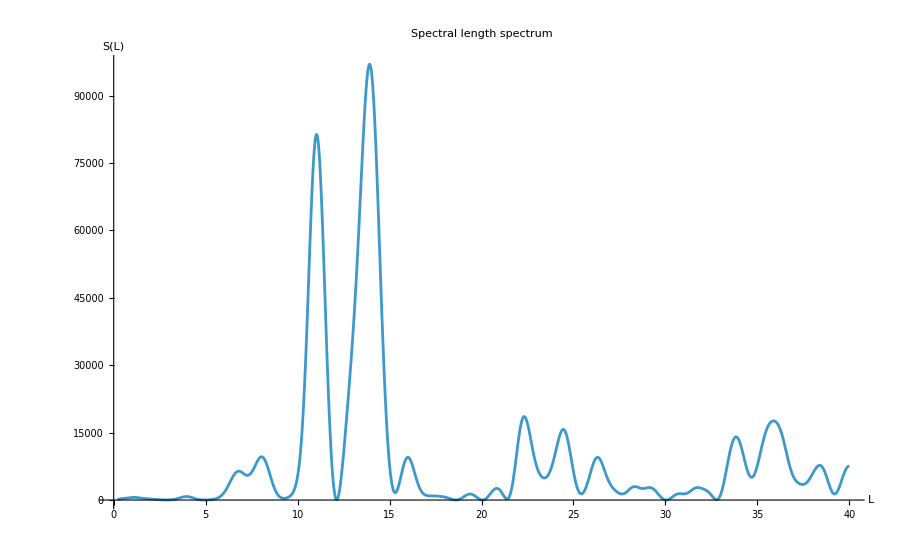

#local maxima found: 20

S(L) min/max: {3.47049,96956.5}

Chosen dominant short peaks La,Lb,Lc = {1.10545,3.9611,6.80348}

Top 12 peaks (L, S):

13.9144 | 96956.5
11.0322 | 81333.1
22.3222 | 18561.2
35.8774 | 17600.7
24.4482 | 15706.5
33.8443 | 14051.6
8.0406 | 9622.07
26.3121 | 9503.38
15.9973 | 9494.82
38.3881 | 7716.38
39.9901 | 7529.34
6.80348 | 6415.75

13.9144 | 96956.5
11.0322 | 81333.1
22.3222 | 18561.2
35.8774 | 17600.7
24.4482 | 15706.5
33.8443 | 14051.6
8.0406 | 9622.07
26.3121 | 9503.38
15.9973 | 9494.82
38.3881 | 7716.38
39.9901 | 7529.34
6.80348 | 6415.75

Candidate fundamentals up to Lcap=10. : {8.0406,6.80348,3.9611,1.10545}

Top candidates by numeric harmonic score (L, score):

6.80348 | If[Total[Boole[{96956.5,2596.21,9503.38}>0]]<1,-10^99,score$93657=hitCount$93657+Total[Log[1+strengths$93657/base$93657]];N[score$93657]]
3.9611 | If[Total[Boole[{9622.07,0.,9494.82}>0]]<1,-10^99,score$93662=hitCount$93662+Total[Log[1+strengths$93662/base$93662]];N[score$93662]]
8.0406 | If[Total[Boole[{9494.82,15706.5,2775.84}>0]]<1,-10^99,score$93652=hitCount$93652+Total[Log[1+strengths$93652/base$93652]];N[score$93652]]
1.10545 | If[Total[Boole[{0.,0.,0.}>0]]<1,-10^99,score$93667=hitCount$93667+Total[Log[1+strengths$93667/base$93667]];N[score$93667]]

ERROR: fewer than 3 harmonic fundamentals found. Increase Lmax or lower minHits.

Reconstructed axes (sorted) from harmonic peaks: reconstructAxesFromPeaks[{1.10545,3.9611,6.80348},2]

Expected axes (sorted): {1.,1.5,2.3}

Chosen dominant short peaks La,Lb,Lc = {1.10545,3.9611,6.80348}

Reconstructed axes (sorted): {0.533725,1.91247,3.2848}

Expected axes (sorted): {1.,1.5,2.3}

```mathematica
Clear["Global`*"];
Needs["NDSolve`FEM`"];

eigenvalueFilePath="C:\\Users\\sulta\\git\\cone-operator-lab\\data\\eigenvalues\\ellipsoid_eigs_a1_b1.5_c2.3_arnoldi-1000.txt";
eigsIndexRange={1,1000};

(*Eigenwerte einlesen*)
targetEigenvaluesRaw=Import[eigenvalueFilePath,"Table"]//Flatten;
targetEigenvaluesSorted=Sort[targetEigenvaluesRaw];
targetEigenvalues=targetEigenvaluesSorted[[eigsIndexRange[[1]];;eigsIndexRange[[2]]]];
numEigs=Length[targetEigenvalues];

Print["N = ",numEigs];
Print["λ_1 = ",First[targetEigenvalues]];
Print["λ_N = ",Last[targetEigenvalues]];

(*Weyl-Fit Koeffizienten (bitte numerisch!)*)
A0fit=N@0.2371691511;
A1fit=N@(-0.5401975968);              (*WAR bei dir String->muss Zahl sein*)
A2fit=N@0.03937795600473376;
volSpec=6 Pi^2 A0fit;
Pspec=(3 volSpec)/(4 Pi);           (*abc*)
Print["V_spec = ",volSpec];
Print["P_spec = abc = ",Pspec];

(*Weyl counting function*)
Nweyl[lam_?NumericQ]:=A0fit lam^(3/2)+A1fit lam+A2fit Sqrt[lam];

(*Fluctuation sequence F_k=k-Nweyl(λ_k)*)
kVals=N@Range[numEigs];
lamVals=N@targetEigenvalues;
Fvals=kVals-(Nweyl/@lamVals);
(*Wavenumbers t_k=sqrt(λ_k)*)
tVals=Sqrt[lamVals];


(*----------------------------*)
(*Spectral length spectrum S(L)*)
(*----------------------------*)

(*Suchbereich für L:anpassen falls Peaks außerhalb liegen*)
Lmin=0.2;
Lmax=40.0;
nL=12000;
Lgrid=Subdivide[Lmin,Lmax,nL];
w=N@Table[0.5 (1-Cos[2 Pi (k-1)/(numEigs-1)]),{k,1,numEigs}];
Fw=Fvals*w;

Print["Window min/max: ",{Min[w],Max[w]}];
Print["Fw min/max: ",{Min[Fw],Max[Fw]}];







Svals=Table[Abs[Total[Fw*Exp[-I*L*tVals]]]^2,{L,Lgrid}];

lenSpecData=Transpose[{Lgrid,Svals}];

Print["Length spectrum computed on ",Length[Lgrid]," grid points."];

(*Plot*)
lenPlot=ListLinePlot[lenSpecData,PlotRange->All,AxesLabel->{"L","S(L)"},PlotLabel->"Spectral length spectrum",ImageSize->900];
lenPlot

(*----------------------------*)(*Robust Peak extraction*)(*----------------------------*)(*Lokale Maxima auf dem ganzen Gitter*)localMaxIdx=Flatten@Position[Table[1<i<Length[Svals]&&Svals[[i]]>Svals[[i-1]]&&Svals[[i]]>Svals[[i+1]],{i,1,Length[Svals]}],True];

Print["#local maxima found: ",Length[localMaxIdx]];
Print["S(L) min/max: ",{Min[Svals],Max[Svals]}];

(*Liste der Peaks (L,S)*)
peaks={Lgrid[[#]],Svals[[#]]}&/@localMaxIdx;

(*Sortiert nach Peak-Höhe*)
peaksSorted=Reverse@SortBy[peaks,Last];

(*Falls extrem viele Peaks:nur die Top M behalten*)
M=Min[200,Length[peaksSorted]];
topPeaks=Take[peaksSorted,M];

(*Aus den Top-Peaks die kürzesten drei L wählen*)
If[Length[topPeaks]<3,Print["ERROR: fewer than 3 peaks found. Try increasing Lmax or reducing nL."];
Print["Try: Lmax=40, nL=12000."];,threeShortestDominant=Take[SortBy[topPeaks,First],3];
{La,Lb,Lc}=threeShortestDominant[[All,1]];
Print["Chosen dominant short peaks La,Lb,Lc = ",{La,Lb,Lc}];];

(*Debug:Top 12 peaks anzeigen*)
Print["Top 12 peaks (L, S):"];
Print[Take[topPeaks,UpTo[12]]//TableForm];

Print[Take[peaksSorted,UpTo[12]]//TableForm];

(*Kandidaten für die drei kürzesten dominanten Peaks:-wir nehmen aus den Top-Peaks die kürzesten drei L-du kannst diese Heuristik später verfeinern*)
topPeaks=Take[peaksSorted,UpTo[30]];


(*-------------------------------*)(*Robust harmonic scoring (numeric)*)(*-------------------------------*)peakL=topPeaks[[All,1]];
peakS=topPeaks[[All,2]];

(*Kandidaten so wählen,dass mMax*L noch im Bereich liegt*)
mMax=4;                       (*prüfe bis 4. Harmonische*)
Lcap=(Max[Lgrid])/mMax;        (*Fundamentals müssen<=Lmax/mMax sein*)
candIdx=Flatten@Position[peakL,x_/;x<=Lcap];
candL=peakL[[candIdx]];

Print["Candidate fundamentals up to Lcap=",N@Lcap," : ",candL];

(*nearest peak strength near target length,relative tolerance*)
nearestStrengthRel[target_?NumericQ,relTol_?NumericQ]:=Module[{idx,tol},tol=relTol*target;
idx=First@Ordering[Abs[peakL-target],1];
If[Abs[peakL[[idx]]-target]<=tol,peakS[[idx]],0.0]];

(*Numeric harmonic score:-counts how many harmonics exist (m=2..mMax)-adds a mild log-strength term,normalized by base strength*)
harmonicScoreNumeric[L_?NumericQ,relTol_?NumericQ,mMax_Integer,minHits_Integer]:=Module[{base,strengths,hitCount,score},base=nearestStrengthRel[L,relTol];
strengths=Table[nearestStrengthRel[m L,relTol],{m,2,mMax}];
hitCount=Total@Boole[strengths>0];
If[base<=0||hitCount<minHits,-10^99,(*harte Strafe statt-Infinity*)score=hitCount+Total[Log[1+strengths/base]];
N@score]];

relTol=0.035;    (*3.5%:nötig wegen sichtbarer Peak-Shift*)
minHits=1;       (*bei nur 14 Peaks:erst mal minHits=1,später erhöhen*)

scores=Table[{L,harmonicScoreNumeric[L,relTol,mMax,minHits]},{L,candL}];
scoresSorted=Reverse@SortBy[scores,Last];

Print["Top candidates by numeric harmonic score (L, score):"];
Print[Take[scoresSorted,UpTo[12]]//TableForm];

(*Drei Fundamentals wählen,nicht zu nah*)
chosen={};
Do[If[Length[chosen]<3&&scoresSorted[[i,2]]>-10^50&&AllTrue[chosen,Abs[#-scoresSorted[[i,1]]]>0.6&],AppendTo[chosen,scoresSorted[[i,1]]]],{i,1,Length[scoresSorted]}];

If[Length[chosen]<3,Print["ERROR: fewer than 3 harmonic fundamentals found. Increase Lmax or lower minHits."],{La,Lb,Lc}=Sort[chosen];
Print["Chosen harmonic fundamentals La,Lb,Lc = ",{La,Lb,Lc}];];


(*Achsen aus den Peaks+Volumenconstraint*)
axesHarmonic=reconstructAxesFromPeaks[{La,Lb,Lc},2];  (*alpha cancels anyway*)
Print["Reconstructed axes (sorted) from harmonic peaks: ",axesHarmonic];
Print["Expected axes (sorted): ",Sort[{1.0,1.5,2.3}]];

threeShortestDominant=Take[SortBy[topPeaks,First],3];
{La,Lb,Lc}=threeShortestDominant[[All,1]];
Print["Chosen dominant short peaks La,Lb,Lc = ",{La,Lb,Lc}];

(*----------------------------*)
(*Axis reconstruction from peaks+volume constraint*)
(*----------------------------*)
reconstructAxesFromPeaks[{Laa_?NumericQ,Lbb_?NumericQ,Lcc_?NumericQ}]:=Module[{VspecLocal,PspecLocal,s},VspecLocal=6 Pi^2 A0fit;
PspecLocal=(3 VspecLocal)/(4 Pi);(*abc*)s=(PspecLocal/(Laa Lbb Lcc))^(1/3);
Sort[{s Laa,s Lbb,s Lcc}]];

If[ValueQ[La]&&ValueQ[Lb]&&ValueQ[Lc],axes=reconstructAxesFromPeaks[{La,Lb,Lc}];
Print["Reconstructed axes (sorted): ",axes];
Print["Expected axes (sorted): ",Sort[{1.0,1.5,2.3}]];];
```